# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\QMB.wl"];
```

MessageName::messg: TranslationEigenvectorRepresentatives::usage cannot be set to FormatUsage[TranslationEigenvectorRepresentatives[L] returns a list of sublists, each containing:  the decimal representation of a bit-string representative eigenvector,  its pseudomomentum k, and the length of its translation orbit,  for a system of ```L``` qubits.]. It must be set to a string.

MessageName::messg: BlockDiagonalize::usage cannot be set to FormatUsage[BlockDiagonalize[matrix,opts] returns ```matrix``` in block-diagonal form. Only 	option is '''Symmetry'''.]. It must be set to a string.

MessageName::messg: Transform::usage cannot be set to FormatUsage[BlockDiagonalize[matrix,opts] returns ```matrix``` in block-diagonal form. Only 	option is '''Symmetry'''.]. It must be set to a string.

General::stop: Further output of MessageName::messg will be suppressed during this calculation.

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]]+I RandomVariate[NormalDistribution[0,1]],{2^L}]];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

```mathematica
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
(*haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]],{2^L}]];*)
(*Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];*)
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]];
```

# Test

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\EntanglementWorkflow3.wl"];
```

```mathematica
Names["EntanglementWorkflow3`*"]
```

{buildExpandFullStateFast,buildMaps,compiledEvolverSector,ExpandBlockVector,ExpandFullState,expandFullStateFastTemplate,makeExpansionMatrix,new,ProjectBlockVector,revIndex,VNentropy}

```mathematica
g=1+GoldenRatio^-3;
```

```mathematica
(*2. Parameters*)
L=8;
J=1;
g=1;
hlist=Sort[Append[Table[10^i,{i,-6,0,0.2}],0.0]];
tlist=Developer`ToPackedArray[Table[10^i,{i,-1,8,0.0025}]];
tlist//Length
hlist//Length
```

3601

32

```mathematica
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
(*3. Build block maps and compiled fast expander*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
```

```mathematica
(*4. Hamiltonian and evolvers*)
h=hlist[[25]];
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*5. Distribute*)
DistributeDefinitions[evenMap,oddMap,ProjectBlockVector,ExpandFullStateFast,tlist,L,new,evenEvolver,oddEvolver];
```

```mathematica
(*6. Define worker on all kernels*)
ParallelEvaluate[entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];];
```

```mathematica
states=Table[RandomChainProductState[L],{10}];
```

```mathematica
states=Table[haarmagnetized[L,-3],{10}];
```

```mathematica
mag=(1/2)IsingHamiltonian[0,1,0,L,BoundaryConditions->"Open"];
```

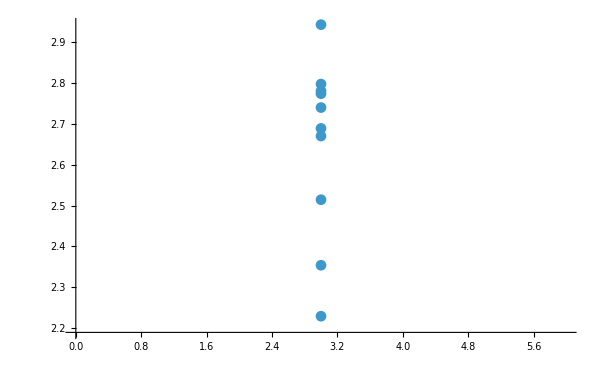

```mathematica
magnetizations=ParallelTable[Chop[Conjugate[i].mag.i],{i,states}];
energies=ParallelTable[Chop[Conjugate[i].Ha.i],{i,states}];
ListPlot[Transpose[{magnetizations,energies}],PlotRange->All,ImageSize->600]
```

```mathematica
(*7. Run computation*)
AbsoluteTiming[originaldata=ParallelTable[entanglementWorker[state],{state,states}];]
```

{1.94932,Null}

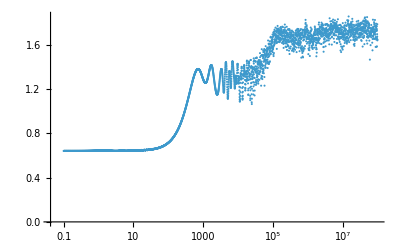

```mathematica
ListLogLinearPlot[Transpose[{tlist,Mean[originaldata]}],PlotRange->All]
```

```mathematica
Clear[haarmagnetized];
haarmagnetized[l_,mz_]:=Module[{nup,dim,sectorIndices,randVec,state},
(*number of spin-up sites*)
nup=Round[mz+l/2];
(*indices of basis states with that magnetization*)
sectorIndices=Select[Range[0,2^l-1],Total[IntegerDigits[#,2,l]]==nup&];
(*dimension of that sector*)
dim=Length[sectorIndices];
(*Haar random complex vector in that sector*)
randVec=RandomVariate[NormalDistribution[],dim]+I RandomVariate[NormalDistribution[],dim];
randVec=Normalize[randVec];
(*full 2^L state with zeros outside the chosen sector*)
state=ConstantArray[0,2^l];
state[[sectorIndices+1]]=randVec;
state];
```

```mathematica
Clear[ProjectorsNAList];
(*returns {Π_A(0),Π_A(1),...,Π_A(LA)};each is 2^LA x 2^LA*)
ProjectorsNAList[LA_Integer?NonNegative]:=Module[{d=2^LA,bits,wts},
bits=IntegerDigits[Range[0,2^LA-1],2,LA];(*left-padded LA-bit strings*)
wts=Total/@bits;(*Hamming weights 0..LA*)
Table[With[{idxs=Pick[Range[d],wts,n]},(*indices with weight=n*)SparseArray[Thread[Rule[Transpose[{idxs,idxs}],1]],(*{{i,i}->1,...}*){d,d}]],{n,0,LA}]];

(*p_{nA}=Tr[Π_nA ρ_A]*)
SectorWeights[rhoA_,projList_List]:=Chop[Tr[#.rhoA]&/@projList,10^(-12)];
(*normalized sector block ρ_A^{(nA)}*)
SectorBlock[rhoA_,proj_]:=Module[{blk=proj.rhoA.proj,p=Chop[Tr[proj.rhoA]]},If[p==0,0,blk/p]];
SectorBlocks[rhoA_,projList_List]:=SectorBlock[rhoA,#]&/@projList;
(*von Neumann entropy of a (sub)density matrix*)
VonNeumannS[m_?MatrixQ]:=Module[{ev=Chop[Eigenvalues[m]]},With[{pos=Select[ev,#>0&]},-Total[pos Log[pos]]]];
(*S=H({p})+Σ p_nA S(ρ_A^{(nA)}) on the block-diagonal (SRE) state*)
SectorEntropySplit[rhoA_,projList_List]:=Module[{ps,blocks,H,Sconf},
ps=SectorWeights[rhoA,projList];
blocks=SectorBlocks[rhoA,projList];
H=With[{p=ps},-Total[Replace[p Log[Replace[p,0->1,{1}]],0.->0.,{1}]]];
Sconf=Total@MapThread[If[#1==0,0,#1*VonNeumannS[#2]]&,{ps,blocks}];
<|"p"->ps,"Snum"->H,"Sconf"->Sconf,"Stotal"->(H+Sconf)|>];
SectorSpectra[rho_,projList_List]:=Table[Module[{P=projList[[n+1]],p},
p=Tr[P.rho];
If[p==0,{n,{}},{n,ReverseSort[Chop[Eigenvalues[(P.rho.P)/p]]]}]],{n,0,La}];
(*assumes:La,projectors={Π0,Π1,...,Π_La},rho,VonNeumannS*)
```

```mathematica
La=Lb=L/2;
```

```mathematica
projectors=ProjectorsNAList[La];
```

```mathematica
projectors//Dimensions
```

{5,16,16}

```mathematica
ini=states[[1]];
```

```mathematica
ini=haar[L];
```

```mathematica
ini=haarmagnetized[L,0];
```

```mathematica
rho=MatrixPartialTrace[Dyad[ini],2,{2^La,2^Lb}];
```

```mathematica
entropies=Chop[SectorEntropySplit[rho,projectors]]
```

<|p→{0.185416,0.445715,0.301646,0.0635964,0.00362573},Snum→1.22975,Sconf→7.06062×10^-18,Stotal→1.22975|>

```mathematica
(*for your evolved ρ_A at some time t*)
res=SectorEntropySplit[rho,projectors];
res["p"]; (*{p_0,p_1,...,p_La}*)
res["Stotal"]; (* =Snum+Sconf*)
```

```mathematica
magA=(1/2)IsingHamiltonian[0,1,0,L/2,BoundaryConditions->"Open"];
```

```mathematica
(*Q_A=(1/2) Sum σ^z_i on A:build once,then*)
CommutatorNorm=Norm[rho.magA-magA.rho,"Frobenius"]
```

1.19114

```mathematica
rhoDeph=Total[(#.rho.#)&/@projectors];
{Stotal,StotalDeph,coherenceGap}=Chop[{VonNeumannS[rho],VonNeumannS[rhoDeph],VonNeumannS[rhoDeph]-VonNeumannS[rho]}];
```

```mathematica
(*column sums (for a quick check:Sum[numC]=Snum,Sum[confC]=Sconf)*)
sumNumC=Total[blockInfo[[All,5]]];
sumConfC=Total[blockInfo[[All,6]]];
sumBoth=sumNumC+sumConfC;
Grid[Join[{{"nA","rank(ρ_nA)","p_nA","S(ρ_nA)","S configuration","S classic"}},Chop[blockInfo]],Frame->All]
{Stotal,StotalDeph,coherenceGap}
```

nA | rank(ρ_nA) | p_nA | S(ρ_nA) | S configuration | S classic
0 | 1 | 0.0148369 | 0 | 0 | 0.0624727
1 | 4 | 0.198484 | 0.973225 | 0.193169 | 0.320958
2 | 6 | 0.575534 | 1.4334 | 0.82497 | 0.317958
3 | 4 | 0.194239 | 0.998716 | 0.19399 | 0.318293
4 | 1 | 0.0169058 | 0 | 0 | 0.0689774

{0,1.22975,1.22975}

# Time evolution workflow

```mathematica
(*6. Define worker on all kernels*)
ParallelEvaluate[evolveworker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}]];];
```

```mathematica
AbsoluteTiming[data=ParallelTable[evolveworker[state],{state,states}];]
```

{1.69732,Null}

```mathematica
rho=Table[MatrixPartialTrace[Dyad[i],2,{2^La,2^Lb}],{i,data[[1]]}];
```

```mathematica
blockInfo=Table[Module[{P=projectors[[n+1]],p,r,rank,Sblk,numC,confC},
p=Tr[P.rho];
r=If[p==0,0,P.rho.P/p];
rank=If[r===0,0,MatrixRank[r]];
Sblk=If[r===0,0,VonNeumannS[r]];
numC=If[p==0,0,-p Log[p]];
(*per-sector number contribution*)
confC=p*Sblk;
(*per-sector configurational contribution*)
{n,rank,p,Sblk,confC,numC}],{n,0,La}];
rhoDeph=Total[(#.rho.#)&/@projectors];
{Stotal,StotalDeph,coherenceGap}=Chop[{VonNeumannS[rho],VonNeumannS[rhoDeph],VonNeumannS[rhoDeph]-VonNeumannS[rho]}];
(*column sums (for a quick check:Sum[numC]=Snum,Sum[confC]=Sconf)*)
sumNumC=Total[blockInfo[[All,5]]];
sumConfC=Total[blockInfo[[All,6]]];
sumBoth=sumNumC+sumConfC;
Grid[Join[{{"nA","rank(ρ_nA)","p_nA","S(ρ_nA)","S configuration","S classic"}},Chop[blockInfo]],Frame->All]
{Stotal,StotalDeph,coherenceGap}
```

```mathematica
Clear[SectorStats];
SectorStats[rhoA_,projs_List]:=Module[{ps,blocks,Sblk,Snum,Sconf,Strue,Sdeph},(*sector weights*)
ps=Tr[#.rhoA]&/@projs;
(*normalized sector blocks (0 if empty)*)
blocks=MapThread[If[#1==0,0,#2.rhoA.#2/#1]&,{ps,projs}];
(*per-sector entropies*)
Sblk=If[#===0,0,VonNeumannS[#]]&/@blocks;
(*number and configurational pieces*)
Snum=-Total@Replace[ps Log@Replace[ps,0->1,{1}],0.->0.,{1}];
Sconf=Total[ps*Sblk];
(*total,dephased total,and coherence gap*)
Strue=VonNeumannS[rhoA];
Sdeph=VonNeumannS[Total[(#.rhoA.#)&/@projs]];
<|"p"->ps,(*vector {p_0,...,p_La}*)"Sblk"->Sblk,(*vector {S(ρ_0),...,S(ρ_La)}*)"Snum"->Snum,"Sconf"->Sconf,"Stotal"->Strue,"Sdeph"->Sdeph,"CohGap"->(Sdeph-Strue)|>];
```

```mathematica
stats=SectorStats[#,projectors]&/@rho;   (*same length as tlist*)
(*time series*)
pMat=stats[[All,"p"]];        (*T x (La+1) matrix of p_{n_A}(t)*)
SnumSeries=stats[[All,"Snum"]];
SconfSeries=stats[[All,"Sconf"]];
StotalSeries=stats[[All,"Stotal"]];
SdephSeries=stats[[All,"Sdeph"]];
CohGapSeries=stats[[All,"CohGap"]];
(*optional:per-sector block entropies S(ρ_{n_A}) over time*)
SblkMat=stats[[All,"Sblk"]];     (*T x (La+1)*)
```

```mathematica
(* =0 by construction*)
(*If H conserves total charge and the global state is in a fixed-charge sector,you should also find CohGapSeries≈0 at all times (block-diagonality).*)
Chop[SdephSeries-(SnumSeries+SconfSeries)];
```

```mathematica
k0=1;  (*e.g.first time,or any index in tlist*)
row=stats[[k0]];
tbl=Transpose@{Range[0,La],(*rank per sector at t_k0*)MapIndexed[With[{k=First@#2},If[row["p"][[k]]==0,0,MatrixRank[(projectors[[k]].rho[[k0]].projectors[[k]])/row["p"][[k]]]]]&,row["p"]],row["p"],row["Sblk"],row["p"]*row["Sblk"],-row["p"]*Log[row["p"]]};
Grid[Join[{{"nA","rank(ρ_nA)","p_nA","S(ρ_nA)","config contrib","number contrib"}},Chop[tbl]],Frame->All]
```

nA | rank(ρ_nA) | p_nA | S(ρ_nA) | config contrib | number contrib
0 | 1 | 0.687865 | 0 | 0 | 0.257373
1 | 3 | 0.312124 | 0.00134518 | 0.000419862 | 0.363423
2 | 4 | 0.0000101547 | 0.000979744 | 9.94905×10^-9 | 0.000116755
3 | 3 | 0 | 0.0010597 | 0 | 2.05104×10^-9
4 | 1 | 0 | 0 | 0 | 0

```mathematica
(*keep only times>0 for log-x plotting*)
posIdx=Flatten@Position[tlist,_?(#>0&)];
tpos=tlist[[posIdx]];
(*helper:pair any y-series with tpos*)
withX[ys_]:=Transpose[{tpos,ys[[posIdx]]}];
(*---probabilities p_{nA}(t):La+1 curves---*)
probCurvesLog=ListLogLinearPlot[withX/@Transpose[pMat],(*pMat is T x (La+1)*)PlotRange->All,Frame->True,FrameLabel->{"t (log scale)","p_{n_A}(t)"},PlotLegends->Placed[LineLegend[ToString/@Range[0,La],LegendLabel->"n_A"],{1,0.35}]];
(*---entropies vs time:S_num,S_conf,S(ρ_A),S(Δ_Q ρ_A),coherence gap---*)
(*entCurvesLog=ListLogLinearPlot[{withX[SnumSeries],withX[SconfSeries],withX[StotalSeries],withX[SdephSeries],withX[CohGapSeries]},PlotRange->All,Frame->True,FrameLabel->{"t (log scale)","entropy (nats)"},PlotLegends->{"S_num","S_conf","S(ρ_A)","S(Δ_Q ρ_A)","coherence gap"}];*)
entCurvesLog=ListLogLinearPlot[{withX[SnumSeries],withX[SconfSeries],withX[StotalSeries]},PlotRange->All,Frame->True,FrameLabel->{"t (log scale)","entropy (nats)"},PlotLegends->{"S_num","S_conf","S(ρ_A)"}];
```

```mathematica
Show[probCurvesLog,ImageSize->700]
```

-Graphics-

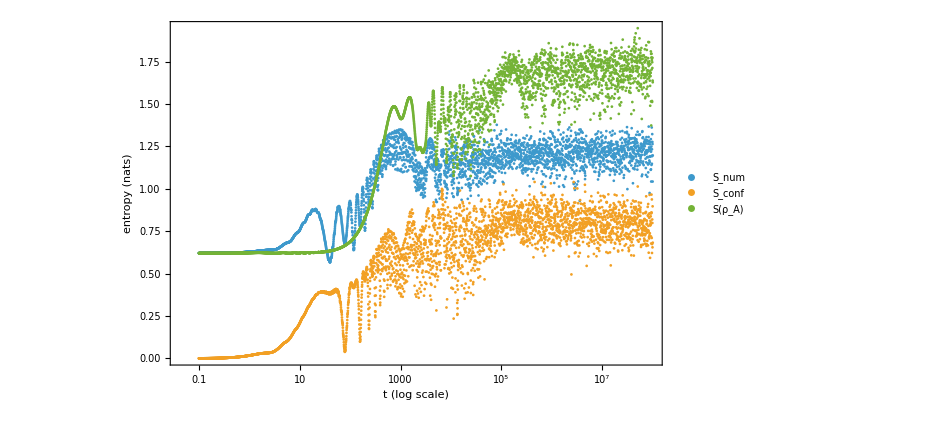

```mathematica
Show[entCurvesLog,ImageSize->700]
```

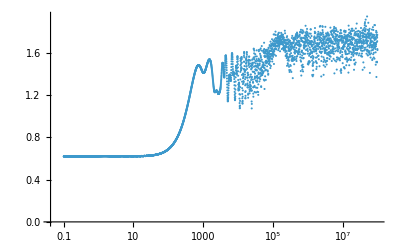

```mathematica
ListLogLinearPlot[Transpose[{tlist,originaldata[[1]]}],PlotRange->All]
```

```mathematica
(*6. Define worker on all kernels*)
ParallelEvaluate[evolveworker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}]];];
```

```mathematica
data=ParallelTable[evolveworker[state],{state,states}]
```

```mathematica
rho=Table[MatrixPartialTrace[Dyad[i],2,{2^La,2^Lb}],{i,data[[1]]}];
```